# Measure meeting angles & test generalized Gibbs–Thomson relation in the 3-species mutual detachment system

Import Comsol simulation of a triple interface junction on a circular domain in the 3-species McRD system with mutual detachment.

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

### Functions for fitting junctions

The interfaces are determined based on the squared norm of the gradient of the total-density fields B (m2+c2) & C (m3+c3).
These gradient fields are evaluated in Comsol and exported on a square grid.
We fit the interfaces by a combination of an arc (for the AB / AC interfaces) with constant curvature and a straight line for the BC interface (due to symmetry of the chosen parameters).
Fitting is done by determining the minimal distance of each point of the square grid to the interface line (arc + straight line; function “pointLoss” below). The loss function is defined as the sum over these distances squared weighted by the value of the squared norm of the gradient. The sum is performed for both the gradients of field B and C and runs in each case over all points on the grid for which the squared norm of the gradient is at least half the maximum value (function “lossCircleLine”). This latter condition excludes weak gradients occuring outside the fitted interface regions.
To account for the offset between the maxima of the gradients of field B and C in the BC interface, a shift dInt is included in the fitting.
To find the minimum of the loss function the Mathematica function FindMinimum is used (function “fitCircleLine”).

```mathematica
ClearAll@pointLoss;
pointLoss[pnt_,x0_,R_,phiInt_,phiLin_]:=Block[{
xint=x0+R{Cos[phiInt],Sin[phiInt]},
eLin={Cos[phiLin],Sin[phiLin]},
eLinN={-Sin[phiLin],Cos[phiLin]},
ePhi={-Sin[phiInt],Cos[phiInt]}*Sign[{Cos[phiLin],Sin[phiLin]}.{-Sin[phiInt],Cos[phiInt]}],
dx,dxLin,dxPhi
},
dx=pnt[[;;2]]-xint;
dxLin=dx.eLin;
dxPhi=dx.ePhi;
pnt[[3]]*
If[dxPhi>=0,
If[dxLin>=0,
(dx.eLinN)^2,
Norm[dx]^2
],
If[dxLin>=0,
Min[{(dx.eLinN)^2,(R-Norm[pnt[[;;2]]-x0])^2}],
(R-Norm[pnt[[;;2]]-x0])^2
]
]
];
```

```mathematica
ClearAll@lossCircleLine;
lossCircleLine[dataSelB_,dataSelC_,xJunc_?VectorQ,dInt_?NumericQ,R_?NumericQ,phiCircleB_?NumericQ,phiLin_?NumericQ]:=Block[{
lossB,
lossC,
x0,(*circle center*)
phiInt,(*angular direction from circle center to intersection point of circle (AB/AC interface) and line (BC interface)*)
eLinN={-Sin[phiLin],Cos[phiLin]}} (*normal vector of the BC interface (pointing in the direction at angle Pi/2+phiLin)*),
x0=xJunc+dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]};
phiInt=phiCircleB-Pi;
lossB=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelB];
x0=xJunc+ReflectionMatrix[eLinN].(dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]});
phiInt=-phiCircleB+2phiLin+Pi;
lossC=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelC];
lossB+lossC(*+1000Max[0,xJunc[[1]]-1000]^2 (*regularization to break degeneracy if junction point leaves the simulation domain at low meeting angles*)*)
];
```

```mathematica
ClearAll@fitCircleLine;
fitCircleLine[dataB_,dataC_,grid_,iniCond_]:=Block[{
xyDataB,
linDataB,
xyDataC,
linDataC,
max,
dataSelB,
dataSelC,
xJunc,(*coord. of junction point*)
x,(*x-coord. of junction*)
y,(*y-coord. of junction*)
dInt,(*normal offset from junction point of BC interface measured by B or C grad. *)
R,(*curvature radius of AB and AC interfaces*)
phiCircleB,(*angular direction from intersection point of circle and line to center of circle*)
phiLin,(*angular direction of line (BC interface)*)
fitRes
},
xyDataB=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataB},{3,1,2}];
(*xyDataB=Table[{indx,indy,dataB[[indy,indx]]},{indx,Length@dataB[[1]]},{indy,Length@dataB}];*)
linDataB=Flatten[xyDataB,1];
max=Max@linDataB[[All,3]];
dataSelB=Select[linDataB,#[[3]]>max/10&]; (*get rid of near-zero values; changed here compared to the case of mutually-suppressed attachment because gradients at AB & AC interfaces become weak*)

xyDataC=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataC},{3,1,2}];
(*xyDataC=Table[{indx,indy,dataC[[indy,indx]]},{indx,Length@dataC[[1]]},{indy,Length@dataC}];*)
linDataC=Flatten[xyDataC,1];
max=Max@linDataC[[All,3]];
dataSelC=Select[linDataC,#[[3]]>max/10&];

fitRes=Last@FindMinimum[
lossCircleLine[dataSelB,dataSelC,{x,y},dInt,100R,phiCircleB,phiLin],
{
{x,First[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{y,Last[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{dInt,dInt/.iniCond,-10,10},
{R,R/100/.iniCond,10^-2,10^2},
{phiCircleB,phiCircleB/.iniCond,0,2Pi},
{phiLin,phiLin/.iniCond,-Pi,Pi}
},AccuracyGoal->5,PrecisionGoal->5];

{
xJunc->({x,y}/.fitRes),
dInt->(dInt/.fitRes),
R->(100R/.fitRes),
phiCircleB->(phiCircleB/.fitRes),
phiLin->(phiLin/.fitRes)
}
];
```

### Functions for measuring the effective interfacial tensions

The effective interfacial tensions are calculated far from the junction from the cross section of the single interfaces.

```mathematica
ClearAll@evalPoints;(*adapt to the geometry of the interfaces (tangent vector of AC interface points towards/away from the junction if center of fitted circle lies right/left of interface)*)
evalPoints[angles_,domainRadius_]:=Quiet[{
{
(xJunc/.angles[[3]])+(domainRadius-xJunc[[1]])/2{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+(domainRadius)/2/R],Sin[phiCircleB+(domainRadius)/2/R]},
{-Sin[phiCircleB+(domainRadius)/2/R],Cos[phiCircleB+(domainRadius)/2/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin-(domainRadius)/2/R],Sin[-phiCircleB+2phiLin-(domainRadius)/2/R]},
{-Sin[-phiCircleB+2phiLin-(domainRadius)/2/R],Cos[-phiCircleB+2phiLin-(domainRadius)/2/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureσ;
measureσ[angles_,dataσ_,grid_]:=Block[{
measurementPoints,
tvecBC,
nvecBC,
tvecAC,
nvecAC,
tvecAB,
nvecAB,
xyData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
BCDomainCorners,
boundaryDist,
junctionDist,
dx=Abs[grid[[1,2,1]]-grid[[1,1,1]]],
L=Max[grid[[1,All,1]]]+Abs[grid[[1,2,1]]-grid[[1,1,1]]]/2
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPoints[angles,L];
tvecBC=measurementPoints[[1,2]];
nvecBC={-#[[2]],#[[1]]}&@measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
nvecAC={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];
nvecAB={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];

xyData=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataσ},{3,1,2}];
dataAC={nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]]),#[[3]]}&/@Select[Flatten[xyData[[Floor[Length[xyData]/2];;]](*These restrictions to certain parts of the data are to make the selection faster. Needs to be changed depending on where the junction is positioned within the data.*),1],((Abs[tvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<2)&&(Abs[nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<1.5))&];

dataAB={nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]]),#[[3]]}&/@Select[Flatten[xyData[[;;Floor[Length[xyData]/2]]],1],((Abs[tvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<2)&&(Abs[nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<1.5))&];
(*determine σAB=σAC as average of the both measurements*)
σABAC=(Total[dataAC[[All,2]]]+Total[dataAB[[All,2]]])*dx^2/8;

BCDomainCorners={#+1.5nvecBC,#-1.5nvecBC}&@measurementPoints[[1,1]]+2tvecBC;
boundaryDist=dist/.FindRoot[Max[Norm/@(BCDomainCorners+dist tvecBC)]==L,{dist,0}];
(*ensure that the edge of the measurement region is at least 1 distant from the junction*)
junctionDist=Norm[measurementPoints[[1,1]]-(xJunc/.angles[[3]])]-2;
If[junctionDist>1,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],((Abs[tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<2)&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/4;,
If[boundaryDist>0,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<2)&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1);,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<(2+boundaryDist))&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1+boundaryDist);
]
];

Print[
ListPlot[{dataAC,dataBC},PlotRange->All]
];
{σABAC,σBC}
];
```

### Functions for measuring the core turnover

To calculate the core turnover, one first calculates the triangular area around the junction core in which the core turnover is calculated.
To this end, the function evalPointsCT uses the junction positions and interface directions fitted above. Assuming the specific layout of the interfaces, it calculates the intersection points of the triangle edges with the interfaces and the tangent vectors of the interfaces at these points.
The function measureCT calculates the core turnover from the modified core turnover by evaluating its integral over the triangular region.

For the test data analyzed here, the branch length used to calculate the core turnover is reduced to 1.5.

```mathematica
ClearAll@evalPointsCT;
evalPointsCT[angles_]:=Quiet[{
{
(xJunc/.angles[[3]])+1.5{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+1.5/R],Sin[phiCircleB+1.5/R]},
{-Sin[phiCircleB+1.5/R],Cos[phiCircleB+1.5/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin-1.5/R],Sin[-phiCircleB+2phiLin-1.5/R]},
{-Sin[-phiCircleB+2phiLin-1.5/R],Cos[-phiCircleB+2phiLin-1.5/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureCT;(*adapt signs of tangent vectors in the triangleTests to the geometry of the interfaces*)
measureCT[angles_,{dataCTx_,dataCTy_},gridCT_]:=Block[{
measurementPoints,
tvecBC,
tvecAC,
tvecAB,
xyData,
triangleTests,
coreData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]](*,
L=Max[gridCT[[1,All,1]]]*)
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPointsCT[angles(*,L*)];
tvecBC=measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
triangleTests=Function[x,And@@((#[[1]].(x-#[[2]])<0)&/@Transpose[{{tvecBC,-tvecAC,tvecAB},measurementPoints[[All,1]]}])];
coreData=Select[xyData,triangleTests[#[[{1,2}]]]&];

{angles[[1]],2{Total[coreData[[All,3]]],
Total[coreData[[All,4]]]}*dx^2}
];
```

### Functions to determine the correction to the core turnover due to interface curvature

The integral of the modified core turnover is calculated far from the junction core over sections of the isolated, curved interfaces. If the interfaces were straight, the integral would vanish. Due to the curvature, it gives a finite contribution which must be subtracted from the integral over the triangular core region determined above.
As the modified core turnover is a vector, the contributions due to interface curvature determined at a distance from the junction must be rotated back by the amount the interface tangent direction changed between the junction position and the evaluation regions. These rotated curvature contributions calculated with measureCTCorr are then subtracted from the integral determined in function measureCT.

```mathematica
ClearAll@evalPointsCTCorr;(*adapt measArclength to the evalPointsCT chosen above to calculate the core turnover & sign of ang to the geometry of the interfaces*)
Options[evalPointsCTCorr]={"measArclength"->4};
evalPointsCTCorr[angles_,{leftMeasurementEdge_,upperMeasurementEdge_},opts:OptionsPattern[]]:=Quiet[
Block[
{arc=OptionValue["measArclength"],ang1=ang/.FindRoot[First[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})/.angles[[3]]]==leftMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang2=ang/.FindRoot[Last[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})/.angles[[3]]]==upperMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang
},
ang=Min[ang1,ang2];
{
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]}),
{-Sin[phiCircleB+ang],Cos[phiCircleB+ang]}
},
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang-arc/R],Sin[phiCircleB+ang-arc/R]}),{-Sin[phiCircleB+ang-arc/R],Cos[phiCircleB+ang-arc/R]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang],Sin[phiCircleB+ang]})),
ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB+ang],Cos[phiCircleB+ang]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB+ang-arc/R],Sin[phiCircleB+ang-arc/R]})),ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB+ang-arc/R],Cos[phiCircleB+ang-arc/R]}
},
ang
}/.angles[[3]]]];
```

```mathematica
ClearAll@measureCTCorr;(*adapt measArclength & rotation matrices to the evalPointsCT chosen above to calculate the core turnover& sign of domainTests to geometry of interfaces*)
Options[measureCTCorr]={"halfStretch"->False,"measurementWidth"->1.5};
measureCTCorr[angles_,{dataCTx_,dataCTy_},gridCT_,opts:OptionsPattern[]]:=Block[{
measurementPoints,
tvecAC1,
tvecAC2,
nvecAC1,
nvecAC2,
tvecAB1,
tvecAB2,
nvecAB1,
nvecAB2,
ang,
xyData,
domainTests,
corrData,
ACcorr,
ABcorr,
corr,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]],
leftMeasurementEdge=Min[gridCT[[1,All,1]]]+1,
upperMeasurementEdge=Max[gridCT[[All,1,2]]]-1
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPointsCTCorr[angles,{leftMeasurementEdge,upperMeasurementEdge},"measArclength"->If[OptionValue["halfStretch"],2,4]];
tvecAC1=measurementPoints[[1,2]];
nvecAC1={#[[2]],-#[[1]]}&@measurementPoints[[1,2]];
tvecAC2=measurementPoints[[2,2]];
nvecAC2={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB1=measurementPoints[[3,2]];
nvecAB1={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];
tvecAB2=measurementPoints[[4,2]];
nvecAB2={#[[2]],-#[[1]]}&@measurementPoints[[4,2]];
ang=measurementPoints[[-1]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
domainTests=Function[x,(tvecAC1.(x-measurementPoints[[1,1]])>0&&tvecAC2.(x-measurementPoints[[2,1]])<0&&(Abs[nvecAC1.(x-measurementPoints[[1,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ACcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

domainTests=Function[x,(tvecAB1.(x-measurementPoints[[3,1]])>0&&tvecAB2.(x-measurementPoints[[4,1]])<0&&(Abs[nvecAB1.(x-measurementPoints[[3,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ABcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

corr=(RotationMatrix[-ang+4/R/.angles[[3]]]+If[OptionValue["halfStretch"],RotationMatrix[-ang+2/R/.angles[[3]]],0]).ACcorr
+
(RotationMatrix[-(-ang+4/R/.angles[[3]])]+If[OptionValue["halfStretch"],RotationMatrix[-(-ang+2/R/.angles[[3]])],0]).ABcorr;

{
angles[[1]],
corr
}
];
```

## Simulation on domain of radius 5

## Import data - mutual detachment system Tuning diffusion coefficient

Prepare exported Comsol data beforehand by: sed -i.bu ‘s/NaN/0/g’ <filename.txt>

Interfaces will be determined from the finite squared norm of the gradients of the total-density fields

```mathematica
dataGrad=Import[NotebookDirectory[]<>"mutualDetachment-NeumannAngles-squareGradients-usageExample.txt","Comsol2DSweep"];
```

```mathematica
dataGradB=dataGrad["((m2x+c2x)^2+(m2y+c2y)^2)"];
```

```mathematica
dataGradC=dataGrad["((m3x+c3x)^2+(m3y+c3y)^2)"];
```

```mathematica
grid=dataGrad["Grid"];
```

Import the field that, integrated across the respective interface, gives the effective interfacial tensions

```mathematica
dataST=Import[NotebookDirectory[]<>"mutualDetachment-NeumannAngles-surfaceTension-usageExample.txt","Comsol2DSweep"];
```

```mathematica
dataσ=dataST["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"];
```

Import fields that are integrated to determine the core contribution T_core

```mathematica
dataCT=Import[NotebookDirectory[]<>"mutualDetachment-NeumannAngles-coreTurnover-usageExample.txt","Comsol2DSweep"];
```

```mathematica
dataCoreTurnoverX=dataCT["(1-Dm1/Dc)*(m1x+c1x)*f1+(1-Dm2/Dc)*(m2x+c2x)*f2+(1-Dm3/Dc)*(m3x+c3x)*f3"];
dataCoreTurnoverY=dataCT["(1-Dm1/Dc)*(m1y+c1y)*f1+(1-Dm2/Dc)*(m2y+c2y)*f2+(1-Dm3/Dc)*(m3y+c3y)*f3"];
```

```mathematica
gridCT=dataCT["Grid"];
```

## Fit interface lines, i.e., the meeting angles at the interface junction

```mathematica
iniCond={xJunc->{-1,0},dInt->0.1,R->750.,phiCircleB->Pi+Pi/6,phiLin->0.};
```

```mathematica
angleList=Block[{fit=0,fitOld,phiCircleB,phiLin},
Table[
Print[dataGrad["SweepValues"][[1,i]]];
fitOld=fit;
fit=fitCircleLine[dataGradB[[i]],dataGradC[[i]],grid,If[i==1,iniCond,Join[{R->Min[100,(R/.fitOld)]},DeleteCases[fitOld,R->_]]]];
(*Show fit result*)
Print[Show[
ListDensityPlot[Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataGradB[[Floor@i,;;;;10,;;;;10]]+dataGradC[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],PlotRange->All,InterpolationOrder->0,AspectRatio->1],
Graphics[{Black,
Circle[((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}),R,{phiCircleB-Pi,Pi}],
Darker@Red,
Line[{((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}),((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]})}],
Black,
Circle[((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]})),R,{Pi,2Pi+Pi-phiCircleB+2phiLin}],
Darker@Red,
Line[{((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]})),((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]}))}]}/.fit]
]];

{
dataGrad["SweepValues"][[1,i]],
3Pi-2phiCircleB/.fit,
fit
},
{i,Range[1,3]}]
];
```

1

FindMinimum::reged: The point {-0.046028,0.000566408,0.0480552,100.,3.63347,-0.00484858} is at the edge of the search region {0.01,100.} in coordinate 4 and the computed search direction points outside the region.

-Graphics-

1.2589

FindMinimum::reged: The point {-0.0443111,-0.000109632,0.0476661,100.,3.63349,-0.00416653} is at the edge of the search region {0.01,100.} in coordinate 4 and the computed search direction points outside the region.

-Graphics-

1.5849

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

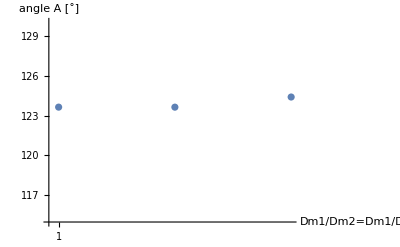

```mathematica
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,130},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"}]
```

#### fitList – expected result

```mathematica
angleList
```

{{1,2.15783,{xJunc→{-0.046028,0.000566408},dInt→0.0480552,R→10000.,phiCircleB→3.63347,phiLin→-0.00484858}},{1.2589,2.15779,{xJunc→{-0.0443111,-0.000109632},dInt→0.0476661,R→10000.,phiCircleB→3.63349,phiLin→-0.00416653}},{1.5849,2.17109,{xJunc→{-0.0581449,-0.00118762},dInt→0.0475415,R→2088.,phiCircleB→3.62684,phiLin→-0.00354171}}}

## Determine effective interfacial tensions σAB, σAC, σBC

Find points on the interfaces that are distant from the junction to measure the effective interfacial tensions.
Around this point, σ is determined by integrating the field dataσ over a rectangle crossing the interface. This integral is then divided by the width of the rectangle.

```mathematica
evalPointsS=evalPoints[#,5]&/@angleList;
```

Show the interface segments used to calculate σ

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataσ[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1
],
Graphics[
Join[{Darker@Red,Thick},Flatten[{
Line[{{#[[1,1]],#[[1,2]]}-2#[[2]],{#[[1,1]],#[[1,2]]}+2#[[2]]}],
Line[{{#[[1,1]],#[[1,2]]}+2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}+2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}],Line[{{#[[1,1]],#[[1,2]]}-2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}-2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}]
}&/@evalPointsS[[Floor@i]],1]]
]
]
,{i,1,Length@angleList}]
```

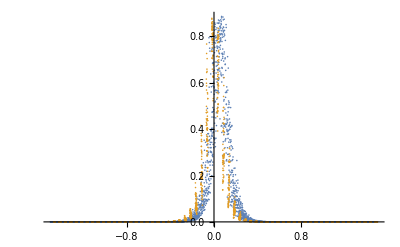

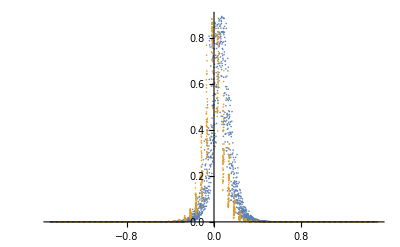

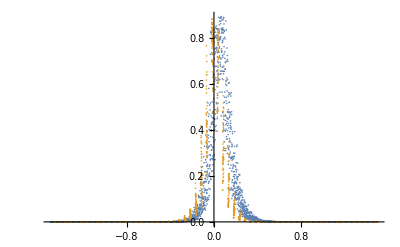

```mathematica
σList=Table[
{angleList[[k,1]],
measureσ[angleList[[k]],dataσ[[k]],grid]
},{k,Length@angleList}];
```

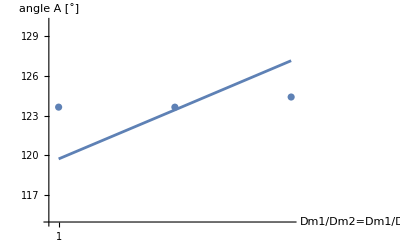

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,130},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList
},
Joined->True]
]
```

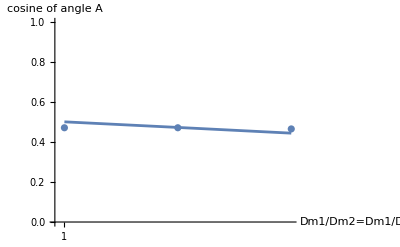

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList
},
Joined->True]
]
```

#### σList – expected result

```mathematica
σList
```

{{1,{0.136826,0.137358}},{1.2589,{0.145141,0.137559}},{1.5849,{0.154079,0.137198}}}

## Core contribution T_core

To determine the x and y components of T_core, we need to integrate the field dataCoreTurnoverX & dataCoreTurnoverY over a triangle whose sides are perpendicular to the three interfaces.
If all interfaces are straight, the triangle can be arbitrarily large because the integrals over a single interface (far from the core region) vanishes.
As two interfaces are curved here, this is not the case and we need to substract the contribution that stems from the interfaces being curved (coreTurnoverCorr).

```mathematica
evalPointsCTS=evalPointsCT/@angleList;
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;10,;;;;10,1]],gridCT[[;;;;10,;;;;10,2]],dataCoreTurnoverX[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTS[[Floor@i]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTS[[Floor@i]]]]
]
,{i,1,Length@angleList}]
```

```mathematica
coreTurnover={};
Monitor[Do[
Block[{ct},
ct=measureCT[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT];
Print[ct];
AppendTo[coreTurnover,ct];
],{k,Length@angleList}];,k]
```

{1,{-0.0249549,-0.00399013}}

{1.2589,{-0.0249833,-0.0113214}}

{1.5849,{-0.0157403,-0.0120184}}

Angle prediction without correcting for interface curvature:

```mathematica
junctionAnglesPred=Table[
Block[{
thetaAB0=phiCircleB-Pi/2/.angleList[[k,3]],
thetaAC0=-phiCircleB+Pi/2+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

{{1,{-2.18542,-0.00484858,2.22637}},{1.2589,{-2.10056,-0.00416653,2.23262}},{1.5849,{-2.01648,-0.00354171,2.16701}}}

```mathematica
angleAPred={#[[1]],(Max[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPred
```

{{1,127.839},{1.2589,128.159},{1.5849,124.363}}

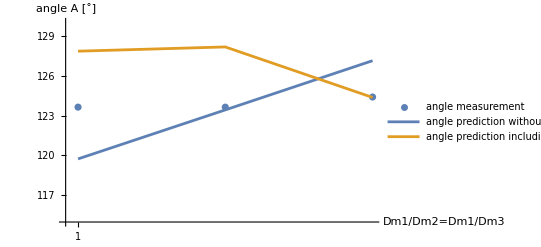

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,130},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "angle A [˚]"},PlotLegends->{"angle measurement"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPred
},
Joined->True,
PlotLegends->{"angle prediction without core contribution","angle prediction including core contribution (without curvature correction)"}]
]
```

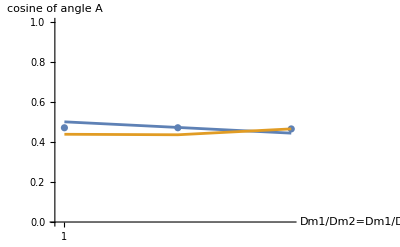

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"Dm1/Dm2=Dm1/Dm3", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPred
},
Joined->True]
]
```

#### Core turnover – expected result

```mathematica
coreTurnover
```

{{1,{-0.0249549,-0.00399013}},{1.2589,{-0.0249833,-0.0113214}},{1.5849,{-0.0157403,-0.0120184}}}

### Correction to core turnover due to curved interfaces

Calculate turnover integral over the curved interface at a distance from the junction, rotate the turnover vector such that that interface piece alines with its contribution in the core-turnover integral and substrate this correction vector from the above calculated turnover vector.

```mathematica
evalPointsCTCorrS=Table[
evalPointsCTCorr[junction,{-1.5,1.5},"measArclength"->1],
{junction,angleList}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;5,;;;;5,1]],gridCT[[;;;;5,;;;;5,2]],dataCoreTurnoverX[[Floor@i,;;;;5,;;;;5]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-2 {-#[[2,2]],#[[2,1]]},#[[1]]+2 {-#[[2,2]],#[[2,1]]}}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-2{-#[[2,2]],#[[2,1]]},#[[1]]-2 {-#[[2,2]],#[[2,1]]}+1#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]],
Line[{#[[1]]+2{-#[[2,2]],#[[2,1]]},#[[1]]+2{-#[[2,2]],#[[2,1]]}+1#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]]
]]
]
,{i,1,Length@angleList}]
```

We need to determine the correction term on a smaller stretch of the interface as the interfaces are too short to measure the full stretch at a certain distance away from the junction.

```mathematica
coreTurnoverCorr={};
Monitor[Do[
Block[{
corr
},
corr=measureCTCorr[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT,"halfStretch"->True,"measurementWidth"->2];
Print[corr];
AppendTo[coreTurnoverCorr,corr];
],{k,1,Length@angleList}];,k]
```

{1,{-0.927992,0.0142969}}

{1.2589,{-0.960787,0.00058658}}

{1.5849,{-0.960311,0.0157413}}

The test data is too coarse to allow for a reliable estimation, giving rise to warnings below.

```mathematica
junctionAnglesPredCorr=Table[
Block[{
thetaAB0=phiCircleB-Pi/2/.angleList[[k,3]],
thetaAC0=-phiCircleB+Pi/2+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]]-coreTurnoverCorr[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

FindRoot::reged: The point {0.105669,0.} is at the edge of the search region {-3.14644,0.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {0.0561023,0.} is at the edge of the search region {-3.14576,0.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {0.182699,0.} is at the edge of the search region {-3.14513,0.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{{1,{0.,-0.00484858,0.105669}},{1.2589,{0.,-0.00416653,0.0561023}},{1.5849,{0.,-0.00354171,0.182699}}}

```mathematica
angleAPredCorr={#[[1]],(Max[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPredCorr
```

{{1,353.946},{1.2589,356.786},{1.5849,349.532}}

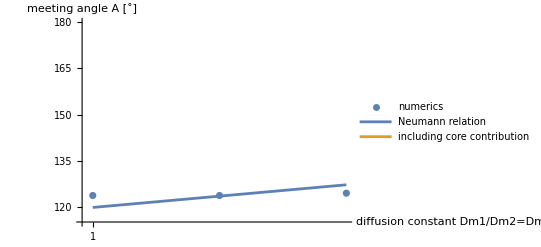

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{115,180},AxesLabel->{"diffusion constant Dm1/Dm2=Dm1/Dm3","meeting angle A [˚]"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

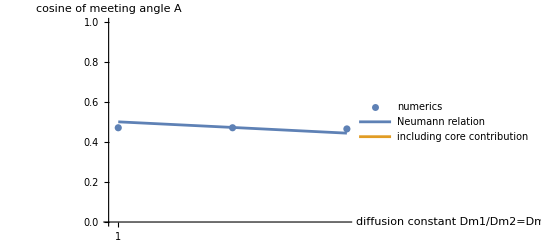

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1},AxesLabel->{"diffusion constant Dm1/Dm2=Dm1/Dm3","cosine of meeting angle A"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

#### Correction list – expected result

```mathematica
coreTurnoverCorr
```

{{1,{-0.927992,0.0142969}},{1.2589,{-0.960787,0.00058658}},{1.5849,{-0.960311,0.0157413}}}